```mathematica
Checkboard=RandomInteger[1,{10,10}]
```

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0)

```mathematica
update[1,2]:=1
```

```mathematica
update[_,3]:=1
```

```mathematica
update[_,_]:=0
```

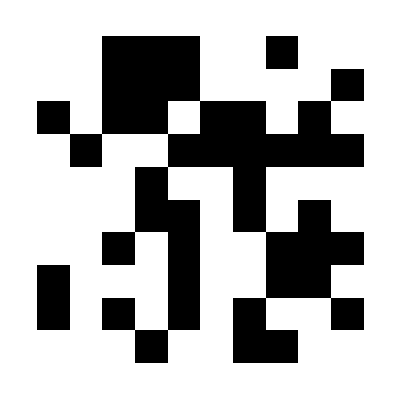

```mathematica
ArrayPlot[Checkboard]
```

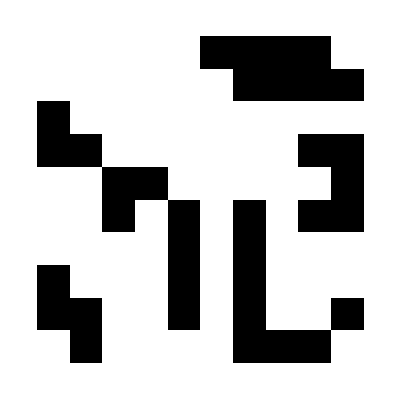

```mathematica
ArrayPlot[Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]]
```

```mathematica
Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]
```

(2 | 1 | 1 | 0 | 1 | 3 | 6 | 8 | 6 | 4
2 | 1 | 0 | 0 | 1 | 3 | 4 | 5 | 4 | 3
4 | 3 | 1 | 0 | 0 | 1 | 2 | 4 | 5 | 6
4 | 3 | 3 | 2 | 1 | 0 | 0 | 1 | 2 | 4
5 | 4 | 3 | 3 | 2 | 2 | 1 | 3 | 5 | 5
2 | 2 | 2 | 5 | 2 | 4 | 1 | 3 | 2 | 2
2 | 2 | 1 | 4 | 2 | 6 | 2 | 4 | 2 | 3
3 | 3 | 1 | 3 | 2 | 6 | 2 | 3 | 1 | 3
4 | 3 | 2 | 2 | 1 | 5 | 3 | 5 | 3 | 3
4 | 2 | 2 | 1 | 2 | 5 | 5 | 6 | 4 | 4)

```mathematica
update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
```

```mathematica
update(({{0, 0, 1, 0}, {1, 1, 0, 0}, {0, 1, 1, 0}}),({{0, 0, 2, 2}, {1, 2, 3, 4}, {3, 3, 1, 1}}))
```

(0 | 0 | 1 | 0
0 | 1 | 1 | 0
1 | 1 | 0 | 0)

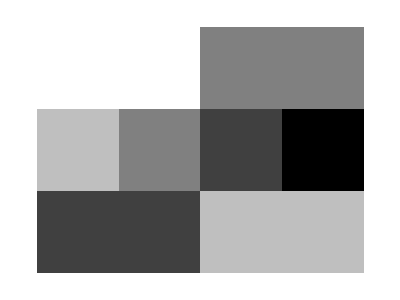

```mathematica
ArrayPlot[({{0, 0, 2, 2}, {1, 2, 3, 4}, {3, 3, 1, 1}})]
```

```mathematica
Checkboard
```

(0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0)

```mathematica
Checkboard=RandomInteger[1,{200,200}];
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update,Listable];
Dynamic[ArrayPlot[Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]]]
```

```mathematica
Checkboard=RandomInteger[1,{20,20}];
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update,Listable];
Dynamic[DynamicModule[{},{ArrayPlot[Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]],Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}];Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]];
ArrayPlot[Checkboard]}]]
```

```mathematica
Checkboard=ImageData[Binarize[-Graphics-]];
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update,Listable];
Dynamic[ArrayPlot[Checkboard=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]]]]
```

```mathematica
f[Checkboard_]:=update[Checkboard,Plus@@Map[RotateRight[Checkboard,#]&,{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}]];
```

```mathematica
Checkboard1=RandomInteger[1,{50,100}];
Checkboard2=Checkboard1;
update[1,2]:=1;
update[_,3]:=1;
update[_,_]:=0;
SetAttributes[update,Listable];
```

```mathematica
While[True,If[Checkboard1≠f[Checkboard2],Checkboard1=Checkboard2;Checkboard2=f[Checkboard2],Checkboard1=Checkboard2=RandomInteger[1,{50,100}];Beep[]]];
```

$Aborted

```mathematica
Dynamic[ArrayPlot[Checkboard1]]
```

```mathematica
If[Checkboard1≠f[Checkboard2],Checkboard1=Checkboard2;Checkboard2=f[Checkboard2],Checkboard1=Checkboard2=RandomInteger[1,{50,100}];Beep[]];
```

```mathematica
Map[ArrayPlot,{Checkboard1,Checkboard2,f[Checkboard2]}]
```

{-Graphics-,-Graphics-,-Graphics-}